Run the below cell to load the library and make sure the Graph outputs are formatted nicely

#### Importing library

```mathematica
Import[NotebookDirectory[]<>"library_graphStates.m"]
```

```mathematica
style={VertexShapeFunction->"Circle",VertexStyle->Directive[EdgeForm[{Thickness[0.01],Black}],LightPurple],EdgeStyle->Directive[Black,Thickness[0.01]],VertexLabels->Placed["Name",{1/2,1/2}],VertexLabelStyle->Directive[Black,FontFamily->"YuMincho",30],VertexSize->0.4,GraphLayout->"CircularEmbedding"};
```

# Graph exploring

#### Some useful initial graphs

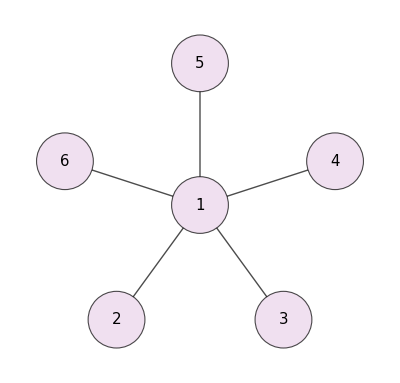
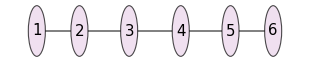
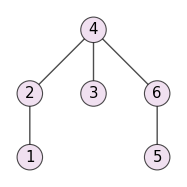
```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

#### Some useful functions for exploring graphs

```mathematica
?FindLUequivalent
```

```mathematica
?Zmeasurement
```

```mathematica
?Xmeasurement
```

```mathematica
?Ymeasurement
```

```mathematica
?LUfamily
```

### JH test

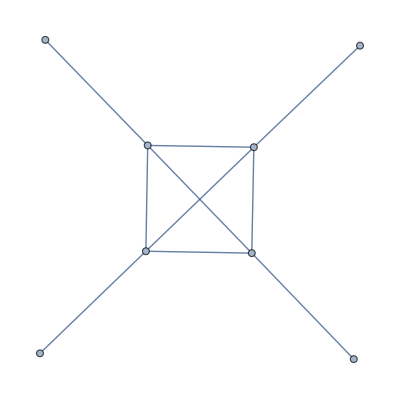

```mathematica
Graph[{1<->2,2<->7,2<->6,2<->3,3<->7,3<->6,3<->4,5<->6,6<->7,7<->8}]
```

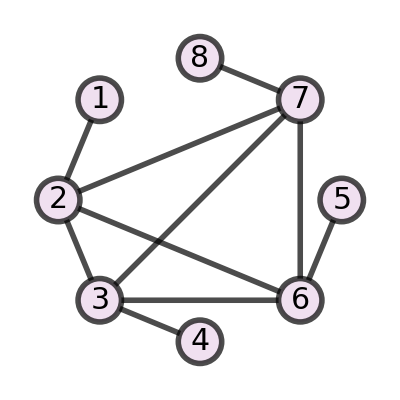

```mathematica
Graph[-Graphics-,style]
```

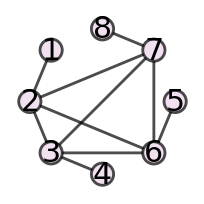
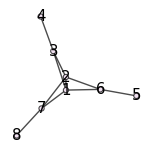
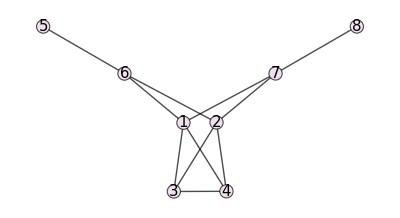
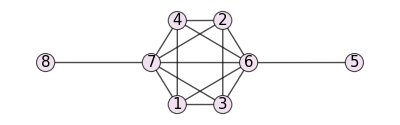
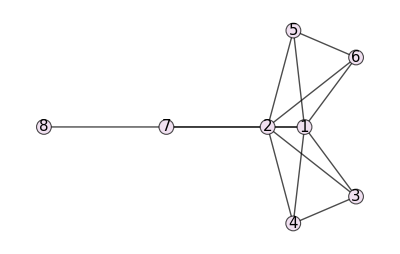
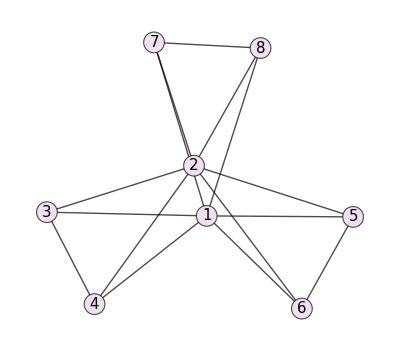
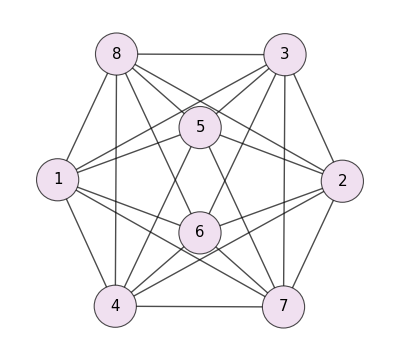

```mathematica
LUfamily[-Graphics-]
```

## Styling arguments

```mathematica
style={
VertexShapeFunction->"Circle"
,VertexStyle->Directive[EdgeForm[{Thickness[0.02],Black,Opacity[1]}],White]
,EdgeStyle->Directive[Black,Thickness[0.02],Opacity[1]]
,VertexLabels->(*Placed["Name",{1/2,1/2}]*)None
,VertexLabelStyle->Directive[Black,FontFamily->"YuMincho",30]
,VertexSize->0.4
,GraphLayout->"CircularEmbedding"
,ImageSize->350};
```

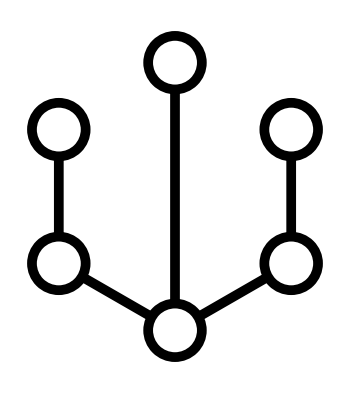

```mathematica
Graph[-Graphics-,style]
```

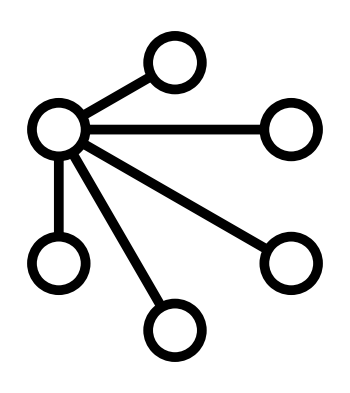

```mathematica
Graph[-Graphics-,style]
```

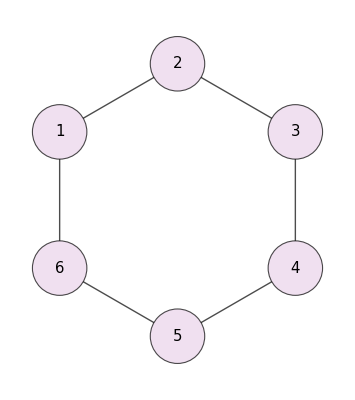
```mathematica
Graph[-Graphics-,style]
```

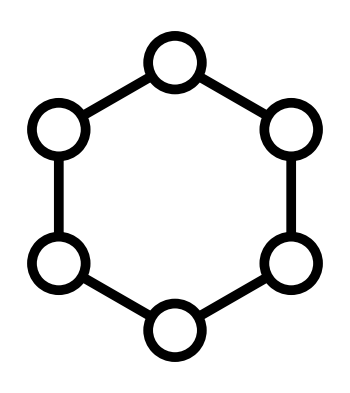

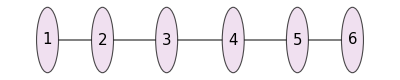
```mathematica
Graph[-Graphics-,style]
```